```mathematica
GenerateValue[M0_,sigma_]:=If[sigma==0,M0,RandomVariate[NormalDistribution[M0,sigma]]]
ΔmProton = 0.00029
mProton=GenerateValue[0.93827208943,ΔmProton]
CoupleEff = GenerateValue[0.0000853727272727272,0.000010835775045318799]
BestYukawa2Cs2Ms6MB2=CoupleEff
ΓMAMI=0.33*10^(-9)
ΔΓMAMI=0.03*10^(-9)
Δα=0.000000017*10^(-3)
α=GenerateValue[7.297525664*10^(-3),Δα]
fK =110.10*10^(-3)
fπ =92.07*10^(-3)
ΔΓtotal=0.05*10^(-6)
Γtotal=GenerateValue[1.31*10^(-6),ΔΓtotal]
ΔBR=0.22*10^(-4)
BR=GenerateValue[2.56*10^(-4),ΔBR]
Δmπ=0.0005*10^(-3)
mπ=GenerateValue[134.9768*10^(-3),Δmπ]
ΔmπA=0.00018*10^(-3)
mπA=GenerateValue[139.57039*10^(-3),ΔmπA]
ΔMη=0.017*10^(-3)
Mη = GenerateValue[547.862*10^(-3),ΔMη]

MηPrime = GenerateValue[957.78*10^(-3),0.06*10^(-3)]

Δmρ=0.23*10^(-3)
mρ=GenerateValue[775.26*10^(-3),Δmρ]
Δmω=0.13*10^(-3)
mω=GenerateValue[782.66*10^(-3),Δmω]
Δmϕ=0.016*10^(-3)
mϕ=GenerateValue[1019.461*10^(-3),Δmϕ]
ΔΓω =0.13*10^(-3)
Γω = GenerateValue[8.68*10^(-3),ΔΓω]
ΔΓρ=0.8*10^(-3)
Γρ = GenerateValue[149.1*10^(-3),ΔΓρ]
ΔΓϕ=0.013*10^(-3)
Γϕ = GenerateValue[4.249*10^(-3),ΔΓϕ]
maZero = 980*10^(-3)
ΔmKP=0.016*10^(-3)
mKP=GenerateValue[493.677*10^(-3),ΔmKP]
mN=GenerateValue[938.27208816*10^(-3),0.00000029*10^(-3)]
Δg=0.01
g =GenerateValue[0.70,Δg]
ΔzSmBm=0.01
zSmBm =GenerateValue[0.65,ΔzSmBm]
ΔϕP=0.5
GenerateValue[41.4,ΔϕP]
ϕP = (GenerateValue[41.4,ΔϕP])Degree
ΔϕV=0.1
ϕV =(GenerateValue[3.3,ΔϕV])Degree
ΔzNS=0.02
zNS = GenerateValue[0.83,ΔzNS]
gρπγ = g/3
gρηγ = g*zNS*Cos[ϕP]
gωπγ = g*Cos[ϕV]
gωηγ =g/3*(zNS*Cos[ϕP]*Cos[ϕV]-2*zSmBm*Sin[ϕP]*Sin[ϕV])
gϕπγ = g*Sin[ϕV]
gϕηγ =g/3*(zNS*Cos[ϕP]*Sin[ϕV]+2*zSmBm*Sin[ϕP]*Cos[ϕV])
cρ = gρπγ*gρηγ
cω = gωπγ*gωηγ
cϕ = gϕπγ*gϕηγ
```

0.00029

0.938601

0.0000960489

0.0000960489

3.3×10^-10

3.×10^-11

1.7×10^-11

0.00729753

0.1101

0.09207

5.×10^-8

1.30082×10^-6

0.000022

0.000249874

5.×10^-7

0.134977

1.8×10^-7

0.139571

0.000017

0.547851

0.957739

0.00023

0.775443

0.00013

0.782628

0.000016

1.01948

0.00013

0.00856852

0.0008

0.148567

0.000013

0.00423316

49/50

0.000016

0.493656

0.938272

0.01

0.705413

0.01

0.641065

0.5

41.1998

0.721629

0.1

0.0589279

0.02

0.853294

0.235138

0.451883

0.704188

0.138637

0.0415444

0.207684

0.106255

0.0976265

0.00862809

```mathematica
Eγ=11
cθ[Eγ_,MX_,tABS_]:=(Eγ tABS+mProton (MX^2+tABS))/(Eγ mProton √(tABS (4+tABS/mProton^2)))
```

11

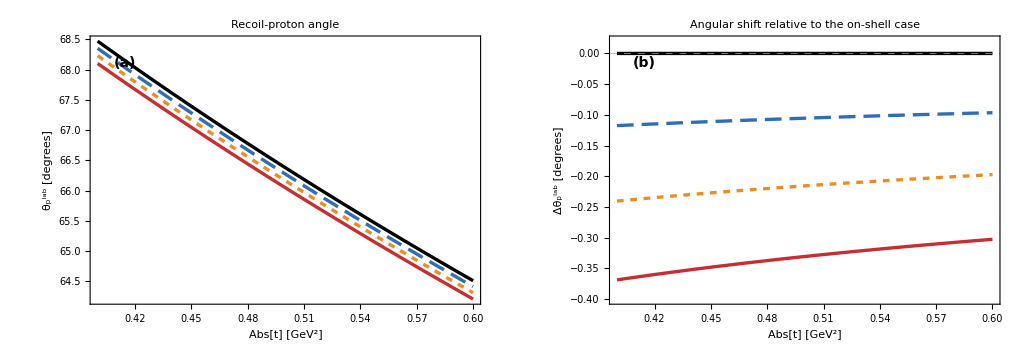

```mathematica
Clear[thetaPDegrees,deltaThetaPDegrees,mEtaReference,massShiftsMeV,masses,curveStyles,legendLabels,absoluteAnglePlot,angularShiftPlot,combinedPlot];

(* ============================================================*)
(*Reference values*)
(* ============================================================*)

mEtaReference=0.547862;

massShiftsMeV={0,25,50,75};

masses=mEtaReference+massShiftsMeV*10^-3;

(* ============================================================*)
(*Proton angle and angular shift,both in degrees*)
(* ============================================================*)

thetaPDegrees[MX_?NumericQ,tABS_?NumericQ]:=ArcCos[Clip[cθ[MX,tABS],{-1,1}]]*180/Pi;

deltaThetaPDegrees[MX_?NumericQ,tABS_?NumericQ]:=thetaPDegrees[MX,tABS]-thetaPDegrees[mEtaReference,tABS];

(* ============================================================*)
(*Plot styles and legends*)
(* ============================================================*)

curveStyles={Directive[Black,AbsoluteThickness[2.4]],Directive[RGBColor[0.18,0.43,0.72],AbsoluteThickness[2.4],Dashing[{0.025,0.012}]],Directive[RGBColor[0.93,0.55,0.12],AbsoluteThickness[2.4],Dashing[{0.010,0.010}]],Directive[RGBColor[0.78,0.18,0.20],AbsoluteThickness[2.4]]};

legendLabels=Row[{Subscript["M","X"]," - ",Subscript["m","η"]," = ",#," MeV"}]&/@massShiftsMeV;

(* ============================================================*)
(*Left panel:absolute proton angle*)
(* ============================================================*)

absoluteAnglePlot=Plot[Evaluate[Table[thetaPDegrees[MX,t],{MX,masses}]],{t,0.4,0.6},Frame->True,Axes->False,FrameLabel->{Style[Row[{Abs[t]," [",Superscript["GeV",2],"]"}],15],Style[Row[{Superscript[Subscript["θ","p"],"lab"]," [degrees]"}],15]},PlotLabel->Style["Recoil-proton angle",15],PlotStyle->curveStyles,PlotRange->{{0.4,0.6},All},PlotRangePadding->Scaled[0.035],FrameStyle->Directive[Black,AbsoluteThickness[1]],FrameTicksStyle->Directive[Black,12],ImageSize->480,AspectRatio->0.72,Epilog->{Inset[Style["(a)",14,Bold],Scaled[{0.09,0.90}]]}];

(* ============================================================*)
(*Right panel:signed angular shift in degrees*)
(* ============================================================*)

angularShiftPlot=Plot[Evaluate[Table[deltaThetaPDegrees[MX,t],{MX,masses}]],{t,0.4,0.6},Frame->True,Axes->False,FrameLabel->{Style[Row[{Abs[t]," [",Superscript["GeV",2],"]"}],15],Style[Row[{"Δ",Superscript[Subscript["θ","p"],"lab"]," [degrees]"}],15]},PlotLabel->Style["Angular shift relative to the on-shell case",15],PlotStyle->curveStyles,PlotRange->{{0.4,0.6},{-0.40,0.02}},PlotRangePadding->Scaled[0.025],GridLines->{None,{0}},GridLinesStyle->Directive[GrayLevel[0.65],Dashed],FrameStyle->Directive[Black,AbsoluteThickness[1]],FrameTicksStyle->Directive[Black,12],ImageSize->480,AspectRatio->0.72,Epilog->{Inset[Style["(b)",14,Bold],Scaled[{0.09,0.90}]]}];

(* ============================================================*)
(*Combined two-panel figure*)
(* ============================================================*)

combinedPlot=Legended[GraphicsRow[{absoluteAnglePlot,angularShiftPlot},Spacings->18,ImageSize->1020],Placed[LineLegend[curveStyles,legendLabels,LegendLayout->"Row",LabelStyle->Directive[13,Black]],Below]];

combinedPlot
```

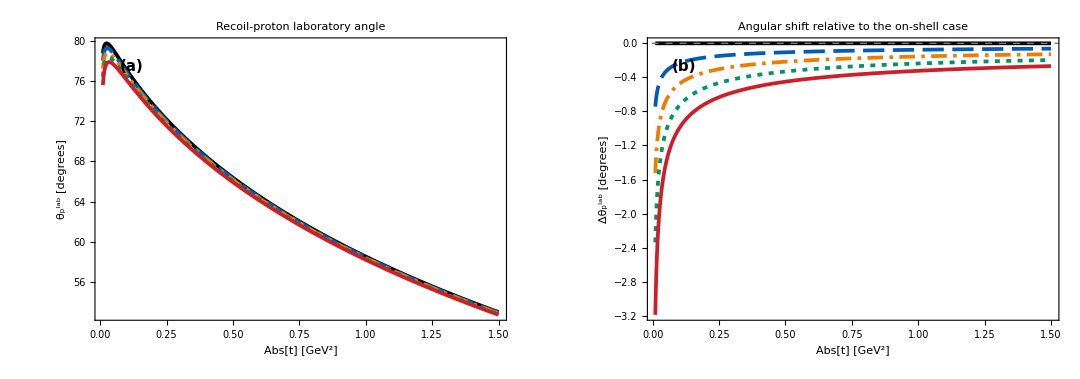
-Graphics-JEF-like kinematics: E_γ = 11 GeV

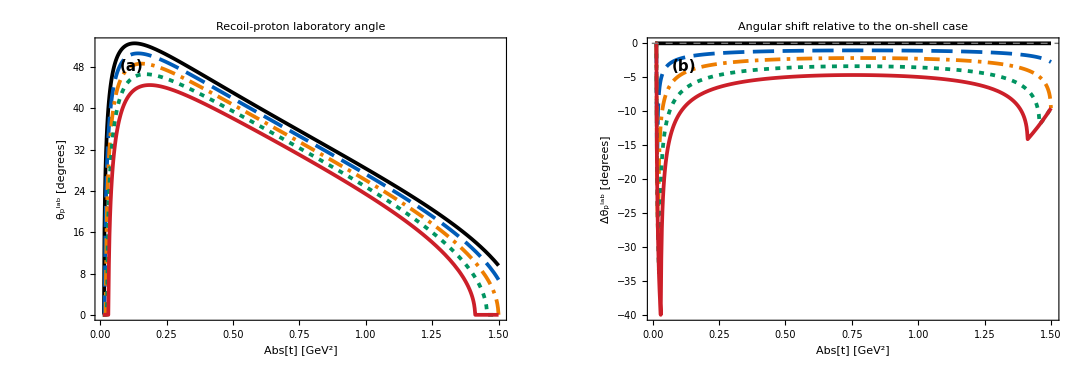
-Graphics-MAMI-like kinematics: E_γ = 1.4 GeV

Grid[{Exported publication-ready files:,C:\Users\balyt\OneDrive\Documents\Recoil_Proton_Angles_JEF_11GeV.pdf,C:\Users\balyt\OneDrive\Documents\Recoil_Proton_Angles_JEF_11GeV.png,C:\Users\balyt\OneDrive\Documents\Recoil_Proton_Angles_MAMI_1p4GeV.pdf,C:\Users\balyt\OneDrive\Documents\Recoil_Proton_Angles_MAMI_1p4GeV.png},Alignment→Left,Spacings→{1,0.55}]

```mathematica
(* ================================================================ *)
(* Recoil-proton laboratory angle for eta photoproduction           *)
(* Separate publication-ready figures for JEF and MAMI kinematics   *)
(* ================================================================ *)

ClearAll[
  cθ, thetaPDegrees, deltaThetaPDegrees, makeAngleFigure,
  exportPublicationFigure, mProton, mEtaReference, massShiftsMeV,
  masses, tMinimum, tMaximum, energyPhotonJEF, energyPhotonMAMI,
  curveStyles, legendLabels, textStyle, frameLabelStyle,
  panelTitleStyle, jefFigure, mamiFigure, outputDirectory,
  exportedFiles
];

(* ================================================================ *)
(* Reference values and displayed ranges                            *)
(* ================================================================ *)

mProton = 0.93827208943;  (* GeV *)
mEtaReference = 0.547862; (* GeV *)

energyPhotonJEF = 11.0;  (* GeV *)
energyPhotonMAMI = 1.4;  (* GeV *)

massShiftsMeV = {0, 25, 50, 75, 100};
masses = mEtaReference + massShiftsMeV*10^-3;

tMinimum = 0.01; (* GeV^2 *)
tMaximum = 1.5; (* GeV^2 *)

(* ================================================================ *)
(* Updated recoil-proton angle                                      *)
(* ================================================================ *)

cθ[energyPhoton_?NumericQ, MX_?NumericQ, tABS_?NumericQ] :=
  (energyPhoton*tABS + mProton*(MX^2 + tABS))/
   (energyPhoton*mProton*Sqrt[tABS*(4 + tABS/mProton^2)]);

thetaPDegrees[
   energyPhoton_?NumericQ, MX_?NumericQ, tABS_?NumericQ] :=
  ArcCos[Clip[cθ[energyPhoton, MX, tABS], {-1, 1}]]*180/Pi;

deltaThetaPDegrees[
   energyPhoton_?NumericQ, MX_?NumericQ, tABS_?NumericQ] :=
  thetaPDegrees[energyPhoton, MX, tABS] -
   thetaPDegrees[energyPhoton, mEtaReference, tABS];

(* ================================================================ *)
(* Saturated, print-safe curve styles and black typography          *)
(* ================================================================ *)

curveStyles = {
  Directive[Black, AbsoluteThickness[2.7]],
  Directive[RGBColor[0.00, 0.36, 0.72], AbsoluteThickness[2.7],
   Dashing[{0.030, 0.012}]],
  Directive[RGBColor[0.93, 0.49, 0.00], AbsoluteThickness[2.7],
   Dashing[{0.022, 0.009, 0.005, 0.009}]],
  Directive[RGBColor[0.00, 0.58, 0.38], AbsoluteThickness[2.7],
   Dashing[{0.007, 0.009}]],
  Directive[RGBColor[0.80, 0.12, 0.16], AbsoluteThickness[2.7]]
};

legendLabels =
  (Row[{
       Subscript[Style["M", Italic], "X"], " - ",
       Subscript[Style["m", Italic], "η"], " = ",
       If[# == 0, "0", Row[{"+", #}]], " MeV"
     }] &) /@ massShiftsMeV;

textStyle = Directive[Black, FontFamily -> "Times", FontSize -> 13];
frameLabelStyle = Directive[Black, FontFamily -> "Times", FontSize -> 16];
panelTitleStyle =
  Directive[Black, Bold, FontFamily -> "Times", FontSize -> 17];

(* ================================================================ *)
(* Build one two-panel figure at a specified photon energy          *)
(* ================================================================ *)

makeAngleFigure[energyPhoton_?NumericQ, experimentLabel_String] :=
 Module[{absoluteAnglePlot, angularShiftPlot, energyDisplay,
   figureTitle},

  energyDisplay =
   If[Abs[energyPhoton - Round[energyPhoton]] < 10^-10,
    Round[energyPhoton], energyPhoton];

  figureTitle =
   Style[
    Row[{experimentLabel, " kinematics: ",
      Subscript[Style["E", Italic], "γ"], " = ",
      energyDisplay, " GeV"}], 18, Bold, Black,
    FontFamily -> "Times"];

  absoluteAnglePlot =
   Plot[
    Evaluate[
     Table[thetaPDegrees[energyPhoton, MX, t], {MX, masses}]],
    {t, tMinimum, tMaximum},
    Frame -> True,
    Axes -> False,
    FrameLabel -> {
      Style[
       Row[{Abs[t], " [", Superscript["GeV", 2], "]"}],
       frameLabelStyle],
      Style[
       Row[{Superscript[Subscript["θ", "p"], "lab"],
         " [degrees]"}], frameLabelStyle]
    },
    PlotLabel ->
     Style["Recoil-proton laboratory angle", panelTitleStyle],
    PlotStyle -> curveStyles,
    PlotRange -> {{tMinimum, tMaximum}, All},
    PlotRangePadding -> {
      {Scaled[0.015], Scaled[0.015]},
      {Scaled[0.055], Scaled[0.055]}
    },
    FrameStyle -> Directive[Black, AbsoluteThickness[1.25]],
    FrameTicksStyle -> Directive[Black, FontFamily -> "Times", 13],
    LabelStyle -> textStyle,
    BaseStyle -> textStyle,
    PlotPoints -> 90,
    MaxRecursion -> 3,
    PerformanceGoal -> "Quality",
    ImageSize -> 510,
    AspectRatio -> 0.72,
    Epilog -> {
      Inset[
       Style["(a)", 15, Bold, Black, FontFamily -> "Times"],
       Scaled[{0.09, 0.90}]]
    }
   ];

  angularShiftPlot =
   Plot[
    Evaluate[
     Table[deltaThetaPDegrees[energyPhoton, MX, t], {MX, masses}]],
    {t, tMinimum, tMaximum},
    Frame -> True,
    Axes -> False,
    FrameLabel -> {
      Style[
       Row[{Abs[t], " [", Superscript["GeV", 2], "]"}],
       frameLabelStyle],
      Style[
       Row[{"Δ",
         Superscript[Subscript["θ", "p"], "lab"],
         " [degrees]"}], frameLabelStyle]
    },
    PlotLabel ->
     Style["Angular shift relative to the on-shell case",
      panelTitleStyle],
    PlotStyle -> curveStyles,
    PlotRange -> {{tMinimum, tMaximum}, All},
    PlotRangePadding -> {
      {Scaled[0.015], Scaled[0.015]},
      {Scaled[0.070], Scaled[0.090]}
    },
    GridLines -> {None, {0}},
    GridLinesStyle ->
     Directive[GrayLevel[0.48], AbsoluteThickness[1.0], Dashed],
    FrameStyle -> Directive[Black, AbsoluteThickness[1.25]],
    FrameTicksStyle -> Directive[Black, FontFamily -> "Times", 13],
    LabelStyle -> textStyle,
    BaseStyle -> textStyle,
    PlotPoints -> 90,
    MaxRecursion -> 3,
    PerformanceGoal -> "Quality",
    ImageSize -> 510,
    AspectRatio -> 0.72,
    Epilog -> {
      Inset[
       Style["(b)", 15, Bold, Black, FontFamily -> "Times"],
       Scaled[{0.09, 0.90}]]
    }
   ];

  Labeled[
   Legended[
    GraphicsRow[
     {absoluteAnglePlot, angularShiftPlot},
     Spacings -> 24,
     ImageSize -> 1080
    ],
    Placed[
     LineLegend[
      curveStyles,
      legendLabels,
      LegendLayout -> "Row",
      LegendMarkerSize -> {38, 14},
      LabelStyle ->
       Directive[Black, FontFamily -> "Times", FontSize -> 14]
     ],
     Below
    ]
   ],
   figureTitle,
   Top
  ]
 ]

(* ================================================================ *)
(* Make the two separate figures                                    *)
(* ================================================================ *)

jefFigure = makeAngleFigure[energyPhotonJEF, "JEF-like"];
mamiFigure = makeAngleFigure[energyPhotonMAMI, "MAMI-like"];

jefFigure
mamiFigure

(* ================================================================ *)
(* Publication-ready export                                         *)
(* PDF is vector; PNG is a 4800-pixel-wide, 600-dpi raster copy.    *)
(* Files are written beside the notebook, or to Directory[] if the  *)
(* notebook has not yet been saved.                                 *)
(* ================================================================ *)

outputDirectory = Quiet@Check[NotebookDirectory[], Directory[]];
If[!StringQ[outputDirectory], outputDirectory = Directory[]];

exportPublicationFigure[figure_, baseName_String] :=
 Module[{pdfPath, pngPath},
  pdfPath = FileNameJoin[{outputDirectory, baseName <> ".pdf"}];
  pngPath = FileNameJoin[{outputDirectory, baseName <> ".png"}];

  Export[pdfPath, figure, "PDF"];
  Export[
   pngPath,
   Rasterize[
    figure,
    "Image",
    RasterSize -> 4800,
    Background -> White
   ],
   "PNG",
   ImageResolution -> 600
  ];

  {pdfPath, pngPath}
 ]

exportedFiles = {
  exportPublicationFigure[
   jefFigure, "Recoil_Proton_Angles_JEF_11GeV"],
  exportPublicationFigure[
   mamiFigure, "Recoil_Proton_Angles_MAMI_1p4GeV"]
};

Grid[
 Prepend[Flatten[exportedFiles],
  "Exported publication-ready files:"],
 Alignment -> Left,
 Spacings -> {1, 0.55}
]
```

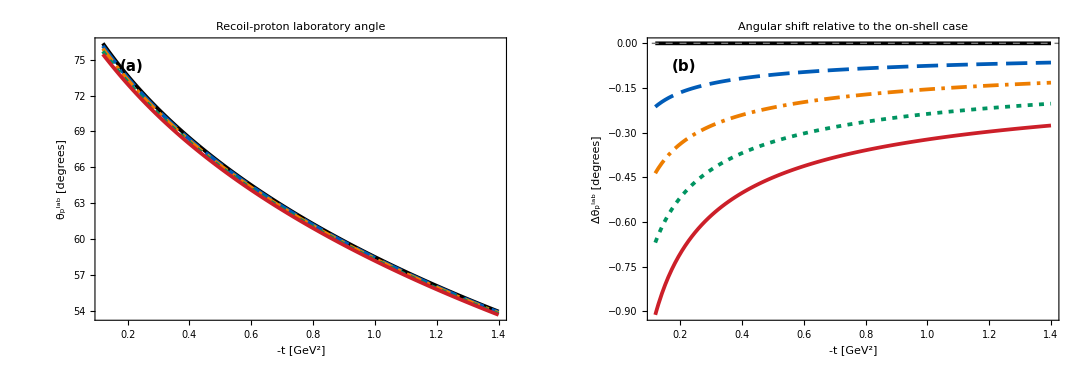
-Graphics-JEF-like kinematics: E_γ = 11 GeV

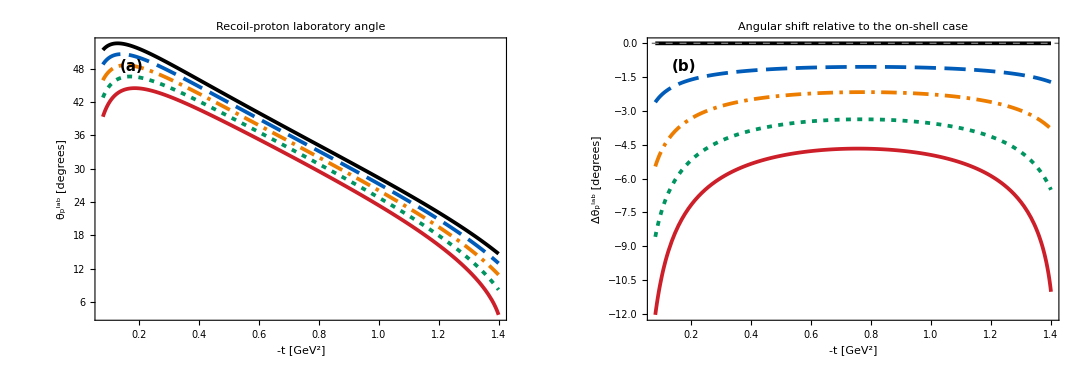
-Graphics-MAMI-like kinematics: E_γ = 1.4 GeV

Mass shift | minimum -t [GeV^2] | maximum -t [GeV^2]
M_X - m_η = 0 MeV | 0.0143 | 1.5779
M_X - m_η = 25 MeV | 0.0176 | 1.5397
M_X - m_η = 50 MeV | 0.0214 | 1.4992
M_X - m_η = 75 MeV | 0.0259 | 1.4565
M_X - m_η = 100 MeV | 0.0313 | 1.4114

Exported publication-ready files:
C:\Users\balyt\OneDrive\Documents\Recoil_Proton_Angles_JEF_11GeV.pdf
C:\Users\balyt\OneDrive\Documents\Recoil_Proton_Angles_JEF_11GeV.png
C:\Users\balyt\OneDrive\Documents\Recoil_Proton_Angles_MAMI_1p4GeV.pdf
C:\Users\balyt\OneDrive\Documents\Recoil_Proton_Angles_MAMI_1p4GeV.png

```mathematica
(* ================================================================*)(*Recoil-proton laboratory angle for eta photoproduction*)(*Separate publication-ready figures for JEF and MAMI kinematics*)(* ================================================================*)ClearAll[cTheta,thetaPDegrees,deltaThetaPDegrees,kallen,tAbsPhysicalRange,makeAngleFigure,exportPublicationFigure,mProton,mEtaReference,massShiftsMeV,masses,energyPhotonJEF,energyPhotonMAMI,tRangeJEF,tRangeMAMI,curveStyles,legendLabels,textStyle,frameLabelStyle,panelTitleStyle,jefFigure,mamiFigure,outputDirectory,exportedFiles,mamiPhysicalRanges,mamiCommonPhysicalRange];

(* ================================================================*)
(*Reference values*)
(* ================================================================*)

mProton=0.93827208943;(*GeV*)mEtaReference=0.547862;(*GeV*)energyPhotonJEF=11.0;(*GeV*)energyPhotonMAMI=1.4;(*GeV*)massShiftsMeV={0,25,50,75,100};
masses=mEtaReference+massShiftsMeV*10^-3;

(*Experimentally sensible displayed ranges.*)
(*Both figures end exactly at-t=1.4 GeV^2.*)

tRangeJEF={0.12,1.40};(*high-efficiency GlueX region*)tRangeMAMI={0.08,1.40};(*populated and detectable region*)(* ================================================================*)(*Exact two-body physical range in-t*)(* ================================================================*)kallen[x_?NumericQ,y_?NumericQ,z_?NumericQ]:=x^2+y^2+z^2-2*x*y-2*x*z-2*y*z;

tAbsPhysicalRange[energyPhoton_?NumericQ,MX_?NumericQ]:=Module[{s,sqrtS,momentumInitial,energyInitialProton,momentumFinal,energyFinalProton,tForward,tBackward},s=mProton^2+2*mProton*energyPhoton;
sqrtS=Sqrt[s];
If[s<(mProton+MX)^2,Return[{Indeterminate,Indeterminate}]];
momentumInitial=(s-mProton^2)/(2*sqrtS);
energyInitialProton=(s+mProton^2)/(2*sqrtS);
momentumFinal=Sqrt[kallen[s,mProton^2,MX^2]]/(2*sqrtS);
energyFinalProton=(s+mProton^2-MX^2)/(2*sqrtS);
tForward=2*mProton^2-2*energyInitialProton*energyFinalProton+2*momentumInitial*momentumFinal;
tBackward=2*mProton^2-2*energyInitialProton*energyFinalProton-2*momentumInitial*momentumFinal;
Sort[{-tForward,-tBackward}]];

(*MAMI ranges for the five displayed masses.*)
(*The common physical range is approximately {0.0313,1.4114}.*)

mamiPhysicalRanges=tAbsPhysicalRange[energyPhotonMAMI,#]&/@masses;

mamiCommonPhysicalRange={Max[mamiPhysicalRanges[[All,1]]],Min[mamiPhysicalRanges[[All,2]]]};

(* ================================================================*)
(*Recoil-proton laboratory angle*)
(* ================================================================*)

cTheta[energyPhoton_?NumericQ,MX_?NumericQ,tABS_?NumericQ]:=(energyPhoton*tABS+mProton*(MX^2+tABS))/(energyPhoton*mProton*Sqrt[tABS*(4+tABS/mProton^2)]);

(*Values outside|cos(theta)| ≤1 are not plotted.*)
(*Clip is used only after the physical-domain test to remove*)
(*insignificant floating-point excursions such as 1+10^-15.*)

thetaPDegrees[energyPhoton_?NumericQ,MX_?NumericQ,tABS_?NumericQ]:=Module[{cosine},cosine=N[cTheta[energyPhoton,MX,tABS]];
If[cosine<-1-10^-10||cosine>1+10^-10,Indeterminate,ArcCos[Clip[cosine,{-1,1}]]*180/Pi]];

deltaThetaPDegrees[energyPhoton_?NumericQ,MX_?NumericQ,tABS_?NumericQ]:=thetaPDegrees[energyPhoton,MX,tABS]-thetaPDegrees[energyPhoton,mEtaReference,tABS];

(* ================================================================*)
(*Saturated,print-safe curve styles and black typography*)
(* ================================================================*)

curveStyles={Directive[Black,AbsoluteThickness[2.7]],Directive[RGBColor[0.00,0.36,0.72],AbsoluteThickness[2.7],Dashing[{0.030,0.012}]],Directive[RGBColor[0.93,0.49,0.00],AbsoluteThickness[2.7],Dashing[{0.022,0.009,0.005,0.009}]],Directive[RGBColor[0.00,0.58,0.38],AbsoluteThickness[2.7],Dashing[{0.007,0.009}]],Directive[RGBColor[0.80,0.12,0.16],AbsoluteThickness[2.7]]};

legendLabels=(Row[{Subscript[Style["M",Italic],"X"]," - ",Subscript[Style["m",Italic],"η"]," = ",If[#==0,"0",Row[{"+",#}]]," MeV"}])&/@massShiftsMeV;

textStyle=Directive[Black,FontFamily->"Times",FontSize->13];

frameLabelStyle=Directive[Black,FontFamily->"Times",FontSize->16];

panelTitleStyle=Directive[Black,Bold,FontFamily->"Times",FontSize->17];

(* ================================================================*)
(*Build one two-panel figure*)
(* ================================================================*)

makeAngleFigure[energyPhoton_?NumericQ,experimentLabel_String,{tMinimum_?NumericQ,tMaximum_?NumericQ}]:=Module[{absoluteAnglePlot,angularShiftPlot,energyDisplay,figureTitle},energyDisplay=If[Abs[energyPhoton-Round[energyPhoton]]<10^-10,Round[energyPhoton],energyPhoton];
figureTitle=Style[Row[{experimentLabel," kinematics: ",Subscript[Style["E",Italic],"γ"]," = ",energyDisplay," GeV"}],18,Bold,Black,FontFamily->"Times"];
absoluteAnglePlot=Plot[Evaluate[Table[thetaPDegrees[energyPhoton,MX,t],{MX,masses}]],{t,tMinimum,tMaximum},Frame->True,Axes->False,FrameLabel->{Style[Row[{"-",Style["t",Italic]," [",Superscript["GeV",2],"]"}],frameLabelStyle],Style[Row[{Superscript[Subscript["θ","p"],"lab"]," [degrees]"}],frameLabelStyle]},PlotLabel->Style["Recoil-proton laboratory angle",panelTitleStyle],PlotStyle->curveStyles,PlotRange->{{tMinimum,tMaximum},All},(*No horizontal padding:the frame ends exactly at 1.4.*)PlotRangePadding->{{0,0},{Scaled[0.055],Scaled[0.055]}},FrameStyle->Directive[Black,AbsoluteThickness[1.25]],FrameTicksStyle->Directive[Black,FontFamily->"Times",FontSize->13],LabelStyle->textStyle,BaseStyle->textStyle,PlotPoints->120,MaxRecursion->4,PerformanceGoal->"Quality",ImageSize->510,AspectRatio->0.72,Epilog->{Inset[Style["(a)",15,Bold,Black,FontFamily->"Times"],Scaled[{0.09,0.90}]]}];
angularShiftPlot=Plot[Evaluate[Table[deltaThetaPDegrees[energyPhoton,MX,t],{MX,masses}]],{t,tMinimum,tMaximum},Frame->True,Axes->False,FrameLabel->{Style[Row[{"-",Style["t",Italic]," [",Superscript["GeV",2],"]"}],frameLabelStyle],Style[Row[{"Δ",Superscript[Subscript["θ","p"],"lab"]," [degrees]"}],frameLabelStyle]},PlotLabel->Style["Angular shift relative to the on-shell case",panelTitleStyle],PlotStyle->curveStyles,PlotRange->{{tMinimum,tMaximum},All},(*No horizontal padding:the frame ends exactly at 1.4.*)PlotRangePadding->{{0,0},{Scaled[0.070],Scaled[0.090]}},GridLines->{None,{0}},GridLinesStyle->Directive[GrayLevel[0.48],AbsoluteThickness[1.0],Dashed],FrameStyle->Directive[Black,AbsoluteThickness[1.25]],FrameTicksStyle->Directive[Black,FontFamily->"Times",FontSize->13],LabelStyle->textStyle,BaseStyle->textStyle,PlotPoints->120,MaxRecursion->4,PerformanceGoal->"Quality",ImageSize->510,AspectRatio->0.72,Epilog->{Inset[Style["(b)",15,Bold,Black,FontFamily->"Times"],Scaled[{0.09,0.90}]]}];
Labeled[Legended[GraphicsRow[{absoluteAnglePlot,angularShiftPlot},Spacings->24,ImageSize->1080],Placed[LineLegend[curveStyles,legendLabels,LegendLayout->"Row",LegendMarkerSize->{38,14},LabelStyle->Directive[Black,FontFamily->"Times",FontSize->14]],Below]],figureTitle,Top]];

(* ================================================================*)
(*Construct figures*)
(* ================================================================*)

jefFigure=makeAngleFigure[energyPhotonJEF,"JEF-like",tRangeJEF];

mamiFigure=makeAngleFigure[energyPhotonMAMI,"MAMI-like",tRangeMAMI];

jefFigure
mamiFigure

(*Optional numerical verification of the MAMI physical domains.*)

Grid[Prepend[MapThread[{Row[{Subscript["M","X"]," - ",Subscript["m","η"]," = ",#1," MeV"}],NumberForm[#2[[1]],{6,4}],NumberForm[#2[[2]],{6,4}]}&,{massShiftsMeV,mamiPhysicalRanges}],{"Mass shift","minimum -t [GeV^2]","maximum -t [GeV^2]"}],Frame->All,Alignment->Center]

(* ================================================================*)
(*Publication-ready export*)
(* ================================================================*)

outputDirectory=Quiet@Check[NotebookDirectory[],Directory[]];

If[!StringQ[outputDirectory],outputDirectory=Directory[]];

exportPublicationFigure[figure_,baseName_String]:=Module[{pdfPath,pngPath},pdfPath=FileNameJoin[{outputDirectory,baseName<>".pdf"}];
pngPath=FileNameJoin[{outputDirectory,baseName<>".png"}];
Export[pdfPath,figure,"PDF"];
Export[pngPath,Rasterize[figure,"Image",RasterSize->4800,Background->White],"PNG",ImageResolution->600];
{pdfPath,pngPath}];

exportedFiles={exportPublicationFigure[jefFigure,"Recoil_Proton_Angles_JEF_11GeV"],exportPublicationFigure[mamiFigure,"Recoil_Proton_Angles_MAMI_1p4GeV"]};

Grid[Prepend[({#}&)/@Flatten[exportedFiles],{"Exported publication-ready files:"}],Alignment->Left,Spacings->{1,0.55}]
```

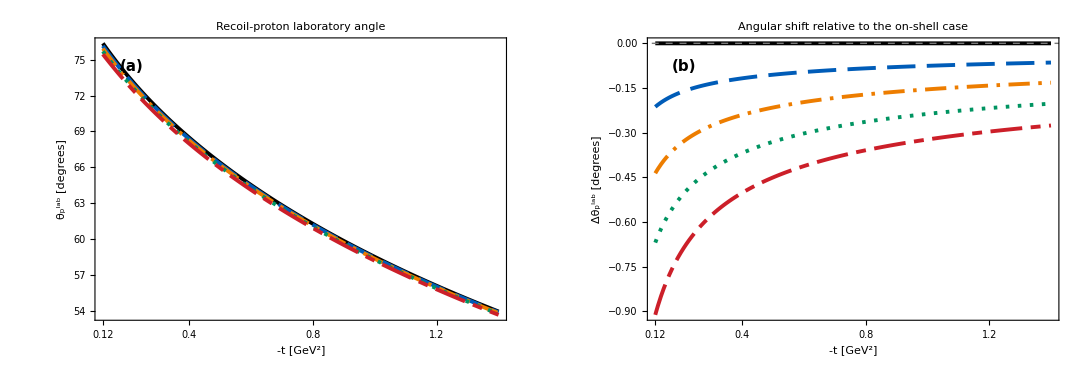
-Graphics-JEF-like kinematics: E_γ = 11 GeV

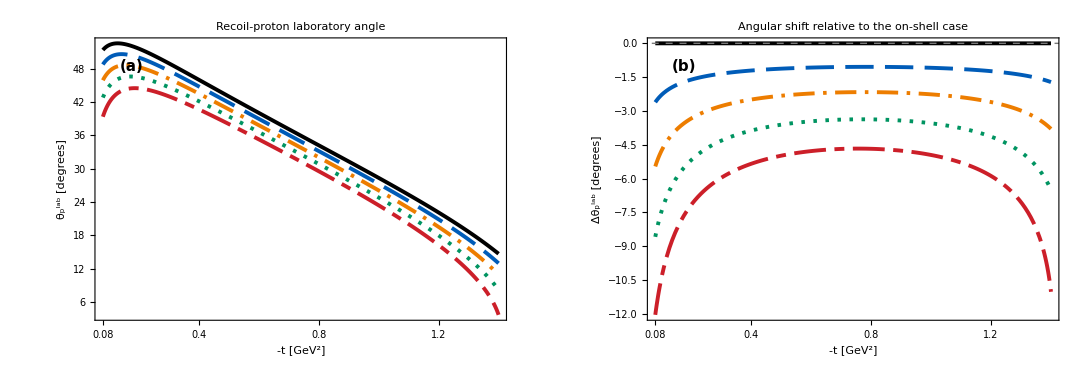
-Graphics-MAMI-like kinematics: E_γ = 1.4 GeV

Mass shift | minimum -t [GeV^2] | maximum -t [GeV^2]
M_X - m_η = 0 MeV | 0.0143 | 1.5779
M_X - m_η = 25 MeV | 0.0176 | 1.5397
M_X - m_η = 50 MeV | 0.0214 | 1.4992
M_X - m_η = 75 MeV | 0.0259 | 1.4565
M_X - m_η = 100 MeV | 0.0313 | 1.4114

Export::noopen: Cannot open C:\Users\balyt\OneDrive\Documents\Recoil_Proton_Angles_JEF_11GeV.pdf.

Exported publication-ready files:
C:\Users\balyt\OneDrive\Documents\Recoil_Proton_Angles_JEF_11GeV.pdf
C:\Users\balyt\OneDrive\Documents\Recoil_Proton_Angles_JEF_11GeV.png
C:\Users\balyt\OneDrive\Documents\Recoil_Proton_Angles_MAMI_1p4GeV.pdf
C:\Users\balyt\OneDrive\Documents\Recoil_Proton_Angles_MAMI_1p4GeV.png

```mathematica
(* ================================================================*)(*Recoil-proton laboratory angle for eta photoproduction*)(*Separate publication-ready figures for JEF and MAMI kinematics*)(* ================================================================*)ClearAll[cTheta,thetaPDegrees,deltaThetaPDegrees,kallen,tAbsPhysicalRange,makeHorizontalTicks,makeAngleFigure,exportPublicationFigure,mProton,mEtaReference,massShiftsMeV,masses,energyPhotonJEF,energyPhotonMAMI,tRangeJEF,tRangeMAMI,curveStyles,legendLabels,textStyle,frameLabelStyle,panelTitleStyle,jefFigure,mamiFigure,outputDirectory,exportedFiles,mamiPhysicalRanges,mamiCommonPhysicalRange];

(* ================================================================*)
(*Reference masses,energies and displayed ranges*)
(* ================================================================*)

mProton=0.93827208943;(*GeV*)mEtaReference=0.547862;(*GeV*)energyPhotonJEF=11.0;(*GeV*)energyPhotonMAMI=1.4;(*GeV*)massShiftsMeV={0,25,50,75,100};

masses=mEtaReference+massShiftsMeV*10^-3;

(*JEF:lower boundary approximately corresponds to the beginning*)
(*of the high-efficiency recoil-proton region.*)

tRangeJEF={0.12,1.40};(*GeV^2*)(*MAMI:representative low-|t|range while retaining the full*)(*common display through-t=1.4 GeV^2.*)tRangeMAMI={0.08,1.40};(*GeV^2*)(* ================================================================*)(*Exact physical two-body range in-t*)(* ================================================================*)kallen[x_?NumericQ,y_?NumericQ,z_?NumericQ]:=x^2+y^2+z^2-2*x*y-2*x*z-2*y*z;

tAbsPhysicalRange[energyPhoton_?NumericQ,MX_?NumericQ]:=Module[{s,sqrtS,momentumInitial,energyInitialProton,momentumFinal,energyFinalProton,tForward,tBackward},s=mProton^2+2*mProton*energyPhoton;
sqrtS=Sqrt[s];
If[s<(mProton+MX)^2,Return[{Indeterminate,Indeterminate}]];
momentumInitial=(s-mProton^2)/(2*sqrtS);
energyInitialProton=(s+mProton^2)/(2*sqrtS);
momentumFinal=Sqrt[kallen[s,mProton^2,MX^2]]/(2*sqrtS);
energyFinalProton=(s+mProton^2-MX^2)/(2*sqrtS);
tForward=2*mProton^2-2*energyInitialProton*energyFinalProton+2*momentumInitial*momentumFinal;
tBackward=2*mProton^2-2*energyInitialProton*energyFinalProton-2*momentumInitial*momentumFinal;
Sort[{-tForward,-tBackward}]];

(*Physical MAMI ranges for all displayed masses.*)

mamiPhysicalRanges=tAbsPhysicalRange[energyPhotonMAMI,#]&/@masses;

mamiCommonPhysicalRange={Max[mamiPhysicalRanges[[All,1]]],Min[mamiPhysicalRanges[[All,2]]]};

(*This evaluates approximately to:*)
(*{0.0313,1.4114} GeV^2.*)
(*Therefore the displayed maximum of 1.4 GeV^2 is physical for*)
(*every curve,including the+100-MeV curve.*)

(* ================================================================*)
(*Recoil-proton laboratory angle*)
(* ================================================================*)

cTheta[energyPhoton_?NumericQ,MX_?NumericQ,tABS_?NumericQ]:=(energyPhoton*tABS+mProton*(MX^2+tABS))/(energyPhoton*mProton*Sqrt[tABS*(4+tABS/mProton^2)]);

(*Nonphysical points are returned as Indeterminate and omitted.*)
(*Clip is applied only after the physical-domain test to remove*)
(*insignificant numerical excursions such as 1+10^-15.*)

thetaPDegrees[energyPhoton_?NumericQ,MX_?NumericQ,tABS_?NumericQ]:=Module[{cosine},cosine=N[cTheta[energyPhoton,MX,tABS]];
If[cosine<-1-10^-10||cosine>1+10^-10,Indeterminate,ArcCos[Clip[cosine,{-1,1}]]*180/Pi]];

deltaThetaPDegrees[energyPhoton_?NumericQ,MX_?NumericQ,tABS_?NumericQ]:=thetaPDegrees[energyPhoton,MX,tABS]-thetaPDegrees[energyPhoton,mEtaReference,tABS];

(* ================================================================*)
(*Saturated colors with independently readable B/W line styles*)
(* ================================================================*)

curveStyles={(*0 MeV:solid black*)Directive[Black,AbsoluteThickness[2.8],CapForm["Round"]],(*+25 MeV:long dashed blue*)Directive[RGBColor[0.00,0.36,0.72],AbsoluteThickness[2.8],Dashing[{0.040,0.016}],CapForm["Round"]],(*+50 MeV:dash-dot orange*)Directive[RGBColor[0.93,0.49,0.00],AbsoluteThickness[2.8],Dashing[{0.030,0.012,0.005,0.012}],CapForm["Round"]],(*+75 MeV:dotted green*)Directive[RGBColor[0.00,0.58,0.38],AbsoluteThickness[2.8],Dashing[{0.005,0.012}],CapForm["Round"]],(*+100 MeV:alternating long-short red dashes*)Directive[RGBColor[0.80,0.12,0.16],AbsoluteThickness[2.8],Dashing[{0.045,0.012,0.014,0.012}],CapForm["Round"]]};

legendLabels=(Row[{Subscript[Style["M",Italic],"X"]," - ",Subscript[Style["m",Italic],"η"]," = ",If[#==0,"0",Row[{"+",#}]]," MeV"}])&/@massShiftsMeV;

(* ================================================================*)
(*Typography*)
(* ================================================================*)

textStyle=Directive[Black,FontFamily->"Times",FontSize->13];

frameLabelStyle=Directive[Black,FontFamily->"Times",FontSize->16];

panelTitleStyle=Directive[Black,Bold,FontFamily->"Times",FontSize->17];

(* ================================================================*)
(*Horizontal ticks*)
(*Includes the precise lower boundary and exact upper value 1.4.*)
(* ================================================================*)

makeHorizontalTicks[tMinimum_?NumericQ]:=Module[{principalValues,minimumLabel},principalValues=N[Range[1/5,7/5,1/5]];
minimumLabel=NumberForm[tMinimum,{3,2},NumberPadding->{"","0"}];
Join[{{tMinimum,minimumLabel}},({#,NumberForm[#,{2,1},NumberPadding->{"","0"}]}&)/@principalValues]];

(* ================================================================*)
(*Construct one two-panel figure*)
(* ================================================================*)

makeAngleFigure[energyPhoton_?NumericQ,experimentLabel_String,{tMinimum_?NumericQ,tMaximum_?NumericQ}]:=Module[{absoluteAnglePlot,angularShiftPlot,energyDisplay,figureTitle,horizontalTicks},energyDisplay=If[Abs[energyPhoton-Round[energyPhoton]]<10^-10,Round[energyPhoton],energyPhoton];
horizontalTicks=makeHorizontalTicks[tMinimum];
figureTitle=Style[Row[{experimentLabel," kinematics: ",Subscript[Style["E",Italic],"γ"]," = ",energyDisplay," GeV"}],18,Bold,Black,FontFamily->"Times"];
(*--------------------------------------------------------------*)(*Panel (a):absolute recoil-proton angle*)(*--------------------------------------------------------------*)absoluteAnglePlot=Plot[Evaluate[Table[thetaPDegrees[energyPhoton,MX,t],{MX,masses}]],{t,tMinimum,tMaximum},Frame->True,Axes->False,FrameLabel->{Style[Row[{"-",Style["t",Italic]," [",Superscript["GeV",2],"]"}],frameLabelStyle],Style[Row[{Superscript[Subscript["θ","p"],"lab"]," [degrees]"}],frameLabelStyle]},FrameTicks->{{Automatic,None},{horizontalTicks,None}},PlotLabel->Style["Recoil-proton laboratory angle",panelTitleStyle],PlotStyle->curveStyles,PlotRange->{{tMinimum,tMaximum},All},(*No horizontal padding:plot ends exactly at 1.4 GeV^2.*)PlotRangePadding->{{0,0},{Scaled[0.055],Scaled[0.055]}},PlotRangeClipping->True,FrameStyle->Directive[Black,AbsoluteThickness[1.25]],FrameTicksStyle->Directive[Black,FontFamily->"Times",FontSize->13],LabelStyle->textStyle,BaseStyle->textStyle,PlotPoints->140,MaxRecursion->4,PerformanceGoal->"Quality",ImageSize->510,AspectRatio->0.72,Epilog->{Inset[Style["(a)",15,Bold,Black,FontFamily->"Times"],Scaled[{0.09,0.90}]]}];
(*--------------------------------------------------------------*)(*Panel (b):angular shift relative to the on-shell case*)(*--------------------------------------------------------------*)angularShiftPlot=Plot[Evaluate[Table[deltaThetaPDegrees[energyPhoton,MX,t],{MX,masses}]],{t,tMinimum,tMaximum},Frame->True,Axes->False,FrameLabel->{Style[Row[{"-",Style["t",Italic]," [",Superscript["GeV",2],"]"}],frameLabelStyle],Style[Row[{"Δ",Superscript[Subscript["θ","p"],"lab"]," [degrees]"}],frameLabelStyle]},FrameTicks->{{Automatic,None},{horizontalTicks,None}},PlotLabel->Style["Angular shift relative to the on-shell case",panelTitleStyle],PlotStyle->curveStyles,PlotRange->{{tMinimum,tMaximum},All},(*No horizontal padding:plot ends exactly at 1.4 GeV^2.*)PlotRangePadding->{{0,0},{Scaled[0.070],Scaled[0.090]}},PlotRangeClipping->True,GridLines->{None,{0}},GridLinesStyle->Directive[GrayLevel[0.48],AbsoluteThickness[1.0],Dashed],FrameStyle->Directive[Black,AbsoluteThickness[1.25]],FrameTicksStyle->Directive[Black,FontFamily->"Times",FontSize->13],LabelStyle->textStyle,BaseStyle->textStyle,PlotPoints->140,MaxRecursion->4,PerformanceGoal->"Quality",ImageSize->510,AspectRatio->0.72,Epilog->{Inset[Style["(b)",15,Bold,Black,FontFamily->"Times"],Scaled[{0.09,0.90}]]}];
(*--------------------------------------------------------------*)(*Assemble the two panels and common legend*)(*--------------------------------------------------------------*)Labeled[Legended[GraphicsRow[{absoluteAnglePlot,angularShiftPlot},Spacings->24,ImageSize->1080],Placed[LineLegend[curveStyles,legendLabels,LegendLayout->"Row",(*Long samples ensure that every dash pattern is visible.*)LegendMarkerSize->{55,14},LabelStyle->Directive[Black,FontFamily->"Times",FontSize->14]],Below]],figureTitle,Top]];

(* ================================================================*)
(*Construct JEF and MAMI figures*)
(* ================================================================*)

jefFigure=makeAngleFigure[energyPhotonJEF,"JEF-like",tRangeJEF];

mamiFigure=makeAngleFigure[energyPhotonMAMI,"MAMI-like",tRangeMAMI];

jefFigure
mamiFigure

(* ================================================================*)
(*Optional numerical verification of the MAMI physical ranges*)
(* ================================================================*)

Grid[Prepend[MapThread[{Row[{Subscript["M","X"]," - ",Subscript["m","η"]," = ",#1," MeV"}],NumberForm[#2[[1]],{6,4}],NumberForm[#2[[2]],{6,4}]}&,{massShiftsMeV,mamiPhysicalRanges}],{"Mass shift","minimum -t [GeV^2]","maximum -t [GeV^2]"}],Frame->All,Alignment->Center,Spacings->{1.2,0.7}]

(* ================================================================*)
(*Publication-ready export*)
(* ================================================================*)

outputDirectory=Quiet@Check[NotebookDirectory[],Directory[]];

If[!StringQ[outputDirectory],outputDirectory=Directory[]];

exportPublicationFigure[figure_,baseName_String]:=Module[{pdfPath,pngPath},pdfPath=FileNameJoin[{outputDirectory,baseName<>".pdf"}];
pngPath=FileNameJoin[{outputDirectory,baseName<>".png"}];
(*Vector publication file.*)Export[pdfPath,figure,"PDF"];
(*High-resolution raster version.*)Export[pngPath,Rasterize[figure,"Image",RasterSize->4800,Background->White],"PNG",ImageResolution->600];
{pdfPath,pngPath}];

exportedFiles={exportPublicationFigure[jefFigure,"Recoil_Proton_Angles_JEF_11GeV"],exportPublicationFigure[mamiFigure,"Recoil_Proton_Angles_MAMI_1p4GeV"]};

Grid[Prepend[({#}&)/@Flatten[exportedFiles],{"Exported publication-ready files:"}],Alignment->Left,Spacings->{1,0.55}]
```

```mathematica
(* ================================================================*)(*Recoil-proton laboratory angle for eta photoproduction*)(*Separate publication-ready figures for JEF and MAMI kinematics*)(* ================================================================*)ClearAll[cTheta,thetaPDegrees,deltaThetaPDegrees,kallen,tAbsPhysicalRange,makeHorizontalTicks,makeAngleFigure,exportPublicationFigure,mProton,mEtaReference,massShiftsMeV,masses,energyPhotonJEF,energyPhotonMAMI,tRangeJEF,tRangeMAMI,curveStyles,legendLabels,textStyle,frameLabelStyle,panelTitleStyle,jefFigure,mamiFigure,outputDirectory,exportedFiles,mamiPhysicalRanges,mamiCommonPhysicalRange];

(* ================================================================*)
(*Reference masses,energies and displayed ranges*)
(* ================================================================*)

mProton=0.93827208943;(*GeV*)mEtaReference=0.547862;(*GeV*)energyPhotonJEF=11.0;(*GeV*)energyPhotonMAMI=1.4;(*GeV*)massShiftsMeV={0,25,50,75,100};

masses=mEtaReference+massShiftsMeV*10^-3;

(*JEF high-efficiency recoil-proton region.*)

tRangeJEF={0.12,1.40};(*GeV^2*)(*MAMI representative range.*)tRangeMAMI={0.08,1.40};(*GeV^2*)(* ================================================================*)(*Exact physical two-body range in-t*)(* ================================================================*)kallen[x_?NumericQ,y_?NumericQ,z_?NumericQ]:=x^2+y^2+z^2-2*x*y-2*x*z-2*y*z;

tAbsPhysicalRange[energyPhoton_?NumericQ,MX_?NumericQ]:=Module[{s,sqrtS,momentumInitial,energyInitialProton,momentumFinal,energyFinalProton,tForward,tBackward},s=mProton^2+2*mProton*energyPhoton;
sqrtS=Sqrt[s];
If[s<(mProton+MX)^2,Return[{Indeterminate,Indeterminate}]];
momentumInitial=(s-mProton^2)/(2*sqrtS);
energyInitialProton=(s+mProton^2)/(2*sqrtS);
momentumFinal=Sqrt[kallen[s,mProton^2,MX^2]]/(2*sqrtS);
energyFinalProton=(s+mProton^2-MX^2)/(2*sqrtS);
tForward=2*mProton^2-2*energyInitialProton*energyFinalProton+2*momentumInitial*momentumFinal;
tBackward=2*mProton^2-2*energyInitialProton*energyFinalProton-2*momentumInitial*momentumFinal;
Sort[{-tForward,-tBackward}]];

(*MAMI physical ranges for all displayed masses.*)

mamiPhysicalRanges=tAbsPhysicalRange[energyPhotonMAMI,#]&/@masses;

mamiCommonPhysicalRange={Max[mamiPhysicalRanges[[All,1]]],Min[mamiPhysicalRanges[[All,2]]]};

(*The common MAMI range is approximately*)
(*0.0313≤-t≤1.4114 GeV^2.*)
(*Therefore,the displayed upper boundary 1.4 GeV^2 is physical*)
(*for all five curves.*)

(* ================================================================*)
(*Recoil-proton laboratory angle*)
(* ================================================================*)

cTheta[energyPhoton_?NumericQ,MX_?NumericQ,tABS_?NumericQ]:=(energyPhoton*tABS+mProton*(MX^2+tABS))/(energyPhoton*mProton*Sqrt[tABS*(4+tABS/mProton^2)]);

(*Nonphysical points are returned as Indeterminate.*)
(*Clip is used only after the physical-domain test to remove*)
(*insignificant numerical excursions around+/-1.*)

thetaPDegrees[energyPhoton_?NumericQ,MX_?NumericQ,tABS_?NumericQ]:=Module[{cosine},cosine=N[cTheta[energyPhoton,MX,tABS]];
If[cosine<-1-10^-10||cosine>1+10^-10,Indeterminate,ArcCos[Clip[cosine,{-1,1}]]*180/Pi]];

deltaThetaPDegrees[energyPhoton_?NumericQ,MX_?NumericQ,tABS_?NumericQ]:=thetaPDegrees[energyPhoton,MX,tABS]-thetaPDegrees[energyPhoton,mEtaReference,tABS];

(* ================================================================*)
(*Saturated colors with independently readable B/W line styles*)
(* ================================================================*)

curveStyles={(*0 MeV:solid black*)Directive[Black,AbsoluteThickness[2.8],CapForm["Round"]],(*+25 MeV:long dashed blue*)Directive[RGBColor[0.00,0.36,0.72],AbsoluteThickness[2.8],Dashing[{0.040,0.016}],CapForm["Round"]],(*+50 MeV:dash-dot orange*)Directive[RGBColor[0.93,0.49,0.00],AbsoluteThickness[2.8],Dashing[{0.030,0.012,0.005,0.012}],CapForm["Round"]],(*+75 MeV:dotted green*)Directive[RGBColor[0.00,0.58,0.38],AbsoluteThickness[2.8],Dashing[{0.005,0.012}],CapForm["Round"]],(*+100 MeV:alternating long-short red dashes*)Directive[RGBColor[0.80,0.12,0.16],AbsoluteThickness[2.8],Dashing[{0.045,0.012,0.014,0.012}],CapForm["Round"]]};

legendLabels=(Row[{Subscript[Style["M",Italic],"X"]," - ",Subscript[Style["m",Italic],"η"]," = ",If[#==0,"0",Row[{"+",#}]]," MeV"}])&/@massShiftsMeV;

(* ================================================================*)
(*Typography*)
(* ================================================================*)

textStyle=Directive[Black,FontFamily->"Times",FontSize->13];

frameLabelStyle=Directive[Black,FontFamily->"Times",FontSize->16];

panelTitleStyle=Directive[Black,Bold,FontFamily->"Times",FontSize->17];

(* ================================================================*)
(*Horizontal ticks*)
(*Includes the exact upper value 1.4.*)
(* ================================================================*)

makeHorizontalTicks[tMinimum_?NumericQ]:=Module[{principalValues,minimumLabel},principalValues=N[Range[1/5,7/5,1/5]];
minimumLabel=NumberForm[tMinimum,{3,2},NumberPadding->{"","0"}];
Join[{{tMinimum,minimumLabel}},({#,NumberForm[#,{2,1},NumberPadding->{"","0"}]}&)/@principalValues]];

(* ================================================================*)
(*Construct one two-panel figure*)
(* ================================================================*)

makeAngleFigure[energyPhoton_?NumericQ,experimentLabel_String,{tMinimum_?NumericQ,tMaximum_?NumericQ}]:=Module[{absoluteAnglePlot,angularShiftPlot,energyDisplay,figureTitle,horizontalTicks},energyDisplay=If[Abs[energyPhoton-Round[energyPhoton]]<10^-10,Round[energyPhoton],energyPhoton];
horizontalTicks=makeHorizontalTicks[tMinimum];
figureTitle=Style[Row[{experimentLabel," kinematics: ",Subscript[Style["E",Italic],"γ"]," = ",energyDisplay," GeV"}],18,Bold,Black,FontFamily->"Times"];
(*--------------------------------------------------------------*)(*Panel (a):absolute recoil-proton angle*)(*--------------------------------------------------------------*)absoluteAnglePlot=Plot[Evaluate[Table[thetaPDegrees[energyPhoton,MX,t],{MX,masses}]],{t,tMinimum,tMaximum},Frame->True,Axes->False,FrameLabel->{Style[Row[{"-",Style["t",Italic]," [",Superscript["GeV",2],"]"}],frameLabelStyle],Style[Row[{Superscript[Subscript["θ","p"],"lab"]," [degrees]"}],frameLabelStyle]},FrameTicks->{{Automatic,None},{horizontalTicks,None}},PlotLabel->Style["Recoil-proton laboratory angle",panelTitleStyle],PlotStyle->curveStyles,PlotRange->{{tMinimum,tMaximum},All},(*No horizontal padding:the frame ends exactly at 1.4.*)PlotRangePadding->{{0,0},{Scaled[0.055],Scaled[0.055]}},PlotRangeClipping->True,FrameStyle->Directive[Black,AbsoluteThickness[1.25]],FrameTicksStyle->Directive[Black,FontFamily->"Times",FontSize->13],LabelStyle->textStyle,BaseStyle->textStyle,PlotPoints->140,MaxRecursion->4,PerformanceGoal->"Quality",ImageSize->510,AspectRatio->0.72,(*Panel label in the bottom-left corner.*)Epilog->{Inset[Style["(a)",15,Bold,Black,FontFamily->"Times",Background->White],Scaled[{0.085,0.095}]]}];
(*--------------------------------------------------------------*)(*Panel (b):angular shift relative to the on-shell case*)(*--------------------------------------------------------------*)angularShiftPlot=Plot[Evaluate[Table[deltaThetaPDegrees[energyPhoton,MX,t],{MX,masses}]],{t,tMinimum,tMaximum},Frame->True,Axes->False,FrameLabel->{Style[Row[{"-",Style["t",Italic]," [",Superscript["GeV",2],"]"}],frameLabelStyle],Style[Row[{"Δ",Superscript[Subscript["θ","p"],"lab"]," [degrees]"}],frameLabelStyle]},FrameTicks->{{Automatic,None},{horizontalTicks,None}},PlotLabel->Style["Angular shift relative to the on-shell case",panelTitleStyle],PlotStyle->curveStyles,PlotRange->{{tMinimum,tMaximum},All},(*No horizontal padding:the frame ends exactly at 1.4.*)PlotRangePadding->{{0,0},{Scaled[0.070],Scaled[0.090]}},PlotRangeClipping->True,GridLines->{None,{0}},GridLinesStyle->Directive[GrayLevel[0.48],AbsoluteThickness[1.0],Dashed],FrameStyle->Directive[Black,AbsoluteThickness[1.25]],FrameTicksStyle->Directive[Black,FontFamily->"Times",FontSize->13],LabelStyle->textStyle,BaseStyle->textStyle,PlotPoints->140,MaxRecursion->4,PerformanceGoal->"Quality",ImageSize->510,AspectRatio->0.72,(*Panel label in the bottom-left corner.*)Epilog->{Inset[Style["(b)",15,Bold,Black,FontFamily->"Times",Background->White],Scaled[{0.085,0.095}]]}];
(*--------------------------------------------------------------*)(*Assemble panels and shared legend*)(*--------------------------------------------------------------*)Labeled[Legended[GraphicsRow[{absoluteAnglePlot,angularShiftPlot},Spacings->24,ImageSize->1080],Placed[LineLegend[curveStyles,legendLabels,LegendLayout->"Row",(*Long samples ensure visibility of all dash patterns.*)LegendMarkerSize->{55,14},LabelStyle->Directive[Black,FontFamily->"Times",FontSize->14]],Below]],figureTitle,Top]];

(* ================================================================*)
(*Construct JEF and MAMI figures*)
(* ================================================================*)

jefFigure=makeAngleFigure[energyPhotonJEF,"JEF-like",tRangeJEF];

mamiFigure=makeAngleFigure[energyPhotonMAMI,"MAMI-like",tRangeMAMI];

jefFigure
mamiFigure

(* ================================================================*)
(*Optional verification of MAMI physical ranges*)
(* ================================================================*)

Grid[Prepend[MapThread[{Row[{Subscript["M","X"]," - ",Subscript["m","η"]," = ",#1," MeV"}],NumberForm[#2[[1]],{6,4}],NumberForm[#2[[2]],{6,4}]}&,{massShiftsMeV,mamiPhysicalRanges}],{"Mass shift","minimum -t [GeV^2]","maximum -t [GeV^2]"}],Frame->All,Alignment->Center,Spacings->{1.2,0.7}]

(* ================================================================*)
(*Publication-ready export*)
(* ================================================================*)

outputDirectory=Quiet@Check[NotebookDirectory[],Directory[]];

If[!StringQ[outputDirectory],outputDirectory=Directory[]];

exportPublicationFigure[figure_,baseName_String]:=Module[{pdfPath,pngPath},pdfPath=FileNameJoin[{outputDirectory,baseName<>".pdf"}];
pngPath=FileNameJoin[{outputDirectory,baseName<>".png"}];
(*Vector PDF.*)Export[pdfPath,figure,"PDF"];
(*High-resolution 600-dpi PNG.*)Export[pngPath,Rasterize[figure,"Image",RasterSize->4800,Background->White],"PNG",ImageResolution->600];
{pdfPath,pngPath}];

exportedFiles={exportPublicationFigure[jefFigure,"Recoil_Proton_Angles_JEF_11GeV"],exportPublicationFigure[mamiFigure,"Recoil_Proton_Angles_MAMI_1p4GeV"]};

Grid[Prepend[({#}&)/@Flatten[exportedFiles],{"Exported publication-ready files:"}],Alignment->Left,Spacings->{1,0.55}]
```

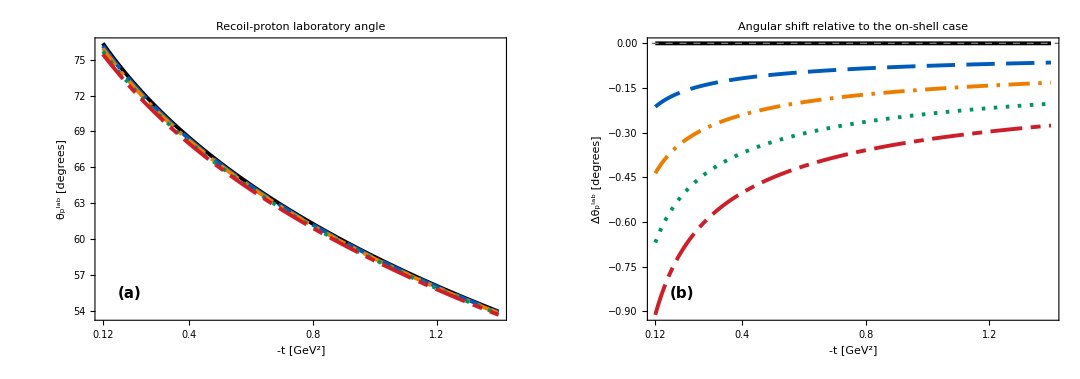
-Graphics-JEF-like kinematics: E_γ = 11 GeV

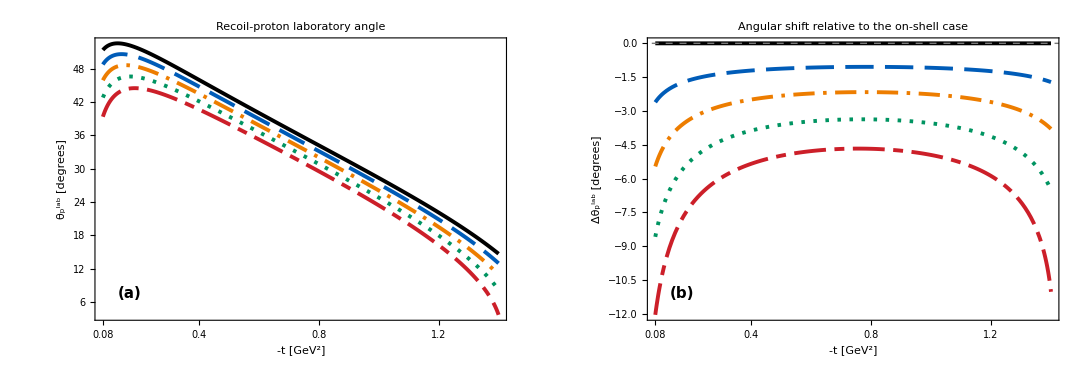
-Graphics-MAMI-like kinematics: E_γ = 1.4 GeV

Mass shift | minimum -t [GeV^2] | maximum -t [GeV^2]
M_X - m_η = 0 MeV | 0.0143 | 1.5779
M_X - m_η = 25 MeV | 0.0176 | 1.5397
M_X - m_η = 50 MeV | 0.0214 | 1.4992
M_X - m_η = 75 MeV | 0.0259 | 1.4565
M_X - m_η = 100 MeV | 0.0313 | 1.4114

Exported publication-ready files:
C:\Users\balyt\OneDrive\Documents\Recoil_Proton_Angles_JEF_11GeV.pdf
C:\Users\balyt\OneDrive\Documents\Recoil_Proton_Angles_JEF_11GeV.png
C:\Users\balyt\OneDrive\Documents\Recoil_Proton_Angles_MAMI_1p4GeV.pdf
C:\Users\balyt\OneDrive\Documents\Recoil_Proton_Angles_MAMI_1p4GeV.png

```mathematica
(* ================================================================*)(*Recoil-proton laboratory angle for eta photoproduction*)(*Separate publication-ready figures for JEF and MAMI kinematics*)(* ================================================================*)ClearAll[cTheta,thetaPDegrees,deltaThetaPDegrees,kallen,tAbsPhysicalRange,makeHorizontalTicks,makeAngleFigure,exportPublicationFigure,mProton,mEtaReference,massShiftsMeV,masses,energyPhotonJEF,energyPhotonMAMI,tRangeJEF,tRangeMAMI,curveStyles,legendLabels,textStyle,frameLabelStyle,panelTitleStyle,jefFigure,mamiFigure,outputDirectory,exportedFiles,mamiPhysicalRanges,mamiCommonPhysicalRange];

(* ================================================================*)
(*Reference masses,energies and displayed ranges*)
(* ================================================================*)

mProton=0.93827208943;(*GeV*)mEtaReference=0.547862;(*GeV*)energyPhotonJEF=11.0;(*GeV*)energyPhotonMAMI=1.4;(*GeV*)massShiftsMeV={0,25,50,75,100};

masses=mEtaReference+massShiftsMeV*10^-3;

(*JEF high-efficiency recoil-proton region.*)

tRangeJEF={0.12,1.40};(*GeV^2*)(*MAMI representative range.*)tRangeMAMI={0.08,1.40};(*GeV^2*)(* ================================================================*)(*Exact physical two-body range in-t*)(* ================================================================*)kallen[x_?NumericQ,y_?NumericQ,z_?NumericQ]:=x^2+y^2+z^2-2*x*y-2*x*z-2*y*z;

tAbsPhysicalRange[energyPhoton_?NumericQ,MX_?NumericQ]:=Module[{s,sqrtS,momentumInitial,energyInitialProton,momentumFinal,energyFinalProton,tForward,tBackward},s=mProton^2+2*mProton*energyPhoton;
sqrtS=Sqrt[s];
If[s<(mProton+MX)^2,Return[{Indeterminate,Indeterminate}]];
momentumInitial=(s-mProton^2)/(2*sqrtS);
energyInitialProton=(s+mProton^2)/(2*sqrtS);
momentumFinal=Sqrt[kallen[s,mProton^2,MX^2]]/(2*sqrtS);
energyFinalProton=(s+mProton^2-MX^2)/(2*sqrtS);
tForward=2*mProton^2-2*energyInitialProton*energyFinalProton+2*momentumInitial*momentumFinal;
tBackward=2*mProton^2-2*energyInitialProton*energyFinalProton-2*momentumInitial*momentumFinal;
Sort[{-tForward,-tBackward}]];

(*MAMI physical ranges for all displayed masses.*)

mamiPhysicalRanges=tAbsPhysicalRange[energyPhotonMAMI,#]&/@masses;

mamiCommonPhysicalRange={Max[mamiPhysicalRanges[[All,1]]],Min[mamiPhysicalRanges[[All,2]]]};

(*The common MAMI range is approximately*)
(*0.0313≤-t≤1.4114 GeV^2.*)
(*Therefore,the displayed upper boundary 1.4 GeV^2 is physical*)
(*for all five curves.*)

(* ================================================================*)
(*Recoil-proton laboratory angle*)
(* ================================================================*)

cTheta[energyPhoton_?NumericQ,MX_?NumericQ,tABS_?NumericQ]:=(energyPhoton*tABS+mProton*(MX^2+tABS))/(energyPhoton*mProton*Sqrt[tABS*(4+tABS/mProton^2)]);

(*Nonphysical points are returned as Indeterminate.*)
(*Clip is used only after the physical-domain test to remove*)
(*insignificant numerical excursions around+/-1.*)

thetaPDegrees[energyPhoton_?NumericQ,MX_?NumericQ,tABS_?NumericQ]:=Module[{cosine},cosine=N[cTheta[energyPhoton,MX,tABS]];
If[cosine<-1-10^-10||cosine>1+10^-10,Indeterminate,ArcCos[Clip[cosine,{-1,1}]]*180/Pi]];

deltaThetaPDegrees[energyPhoton_?NumericQ,MX_?NumericQ,tABS_?NumericQ]:=thetaPDegrees[energyPhoton,MX,tABS]-thetaPDegrees[energyPhoton,mEtaReference,tABS];

(* ================================================================*)
(*Saturated colors with independently readable B/W line styles*)
(* ================================================================*)

curveStyles={(*0 MeV:solid black*)Directive[Black,AbsoluteThickness[2.8],CapForm["Round"]],(*+25 MeV:long dashed blue*)Directive[RGBColor[0.00,0.36,0.72],AbsoluteThickness[2.8],Dashing[{0.040,0.016}],CapForm["Round"]],(*+50 MeV:dash-dot orange*)Directive[RGBColor[0.93,0.49,0.00],AbsoluteThickness[2.8],Dashing[{0.030,0.012,0.005,0.012}],CapForm["Round"]],(*+75 MeV:dotted green*)Directive[RGBColor[0.00,0.58,0.38],AbsoluteThickness[2.8],Dashing[{0.005,0.012}],CapForm["Round"]],(*+100 MeV:alternating long-short red dashes*)Directive[RGBColor[0.80,0.12,0.16],AbsoluteThickness[2.8],Dashing[{0.045,0.012,0.014,0.012}],CapForm["Round"]]};

legendLabels=(Row[{Subscript[Style["M",Italic],"X"]," - ",Subscript[Style["m",Italic],"η"]," = ",If[#==0,"0",Row[{"+",#}]]," MeV"}])&/@massShiftsMeV;

(* ================================================================*)
(*Typography*)
(* ================================================================*)

textStyle=Directive[Black,FontFamily->"Times",FontSize->13];

frameLabelStyle=Directive[Black,FontFamily->"Times",FontSize->16];

panelTitleStyle=Directive[Black,Bold,FontFamily->"Times",FontSize->17];

(* ================================================================*)
(*Horizontal ticks*)
(*Includes the exact upper value 1.4.*)
(* ================================================================*)

makeHorizontalTicks[tMinimum_?NumericQ]:=Module[{principalValues,minimumLabel},principalValues=N[Range[1/5,7/5,1/5]];
minimumLabel=NumberForm[tMinimum,{3,2},NumberPadding->{"","0"}];
Join[{{tMinimum,minimumLabel}},({#,NumberForm[#,{2,1},NumberPadding->{"","0"}]}&)/@principalValues]];

(* ================================================================*)
(*Construct one two-panel figure*)
(* ================================================================*)

makeAngleFigure[energyPhoton_?NumericQ,experimentLabel_String,{tMinimum_?NumericQ,tMaximum_?NumericQ}]:=Module[{absoluteAnglePlot,angularShiftPlot,energyDisplay,figureTitle,horizontalTicks},energyDisplay=If[Abs[energyPhoton-Round[energyPhoton]]<10^-10,Round[energyPhoton],energyPhoton];
horizontalTicks=makeHorizontalTicks[tMinimum];
figureTitle=Style[Row[{experimentLabel," kinematics: ",Subscript[Style["E",Italic],"γ"]," = ",energyDisplay," GeV"}],18,Bold,Black,FontFamily->"Times"];
(*--------------------------------------------------------------*)(*Panel (a):absolute recoil-proton angle*)(*--------------------------------------------------------------*)absoluteAnglePlot=Plot[Evaluate[Table[thetaPDegrees[energyPhoton,MX,t],{MX,masses}]],{t,tMinimum,tMaximum},Frame->True,Axes->False,FrameLabel->{Style[Row[{"-",Style["t",Italic]," [",Superscript["GeV",2],"]"}],frameLabelStyle],Style[Row[{Superscript[Subscript["θ","p"],"lab"]," [degrees]"}],frameLabelStyle]},FrameTicks->{{Automatic,None},{horizontalTicks,None}},PlotLabel->Style["Recoil-proton laboratory angle",panelTitleStyle],PlotStyle->curveStyles,PlotRange->{{tMinimum,tMaximum},All},(*No horizontal padding:the frame ends exactly at 1.4.*)PlotRangePadding->{{0,0},{Scaled[0.055],Scaled[0.055]}},PlotRangeClipping->True,FrameStyle->Directive[Black,AbsoluteThickness[1.25]],FrameTicksStyle->Directive[Black,FontFamily->"Times",FontSize->13],LabelStyle->textStyle,BaseStyle->textStyle,PlotPoints->140,MaxRecursion->4,PerformanceGoal->"Quality",ImageSize->510,AspectRatio->0.72,(*Panel label in the bottom-left corner.*)Epilog->{Inset[Style["(a)",15,Bold,Black,FontFamily->"Times",Background->White],Scaled[{0.085,0.095}]]}];
(*--------------------------------------------------------------*)(*Panel (b):angular shift relative to the on-shell case*)(*--------------------------------------------------------------*)angularShiftPlot=Plot[Evaluate[Table[deltaThetaPDegrees[energyPhoton,MX,t],{MX,masses}]],{t,tMinimum,tMaximum},Frame->True,Axes->False,FrameLabel->{Style[Row[{"-",Style["t",Italic]," [",Superscript["GeV",2],"]"}],frameLabelStyle],Style[Row[{"Δ",Superscript[Subscript["θ","p"],"lab"]," [degrees]"}],frameLabelStyle]},FrameTicks->{{Automatic,None},{horizontalTicks,None}},PlotLabel->Style["Angular shift relative to the on-shell case",panelTitleStyle],PlotStyle->curveStyles,PlotRange->{{tMinimum,tMaximum},All},(*No horizontal padding:the frame ends exactly at 1.4.*)PlotRangePadding->{{0,0},{Scaled[0.070],Scaled[0.090]}},PlotRangeClipping->True,GridLines->{None,{0}},GridLinesStyle->Directive[GrayLevel[0.48],AbsoluteThickness[1.0],Dashed],FrameStyle->Directive[Black,AbsoluteThickness[1.25]],FrameTicksStyle->Directive[Black,FontFamily->"Times",FontSize->13],LabelStyle->textStyle,BaseStyle->textStyle,PlotPoints->140,MaxRecursion->4,PerformanceGoal->"Quality",ImageSize->510,AspectRatio->0.72,(*Panel label in the bottom-left corner.*)Epilog->{Inset[Style["(b)",15,Bold,Black,FontFamily->"Times",Background->White],Scaled[{0.085,0.095}]]}];
(*--------------------------------------------------------------*)(*Assemble panels and shared legend*)(*--------------------------------------------------------------*)Labeled[Legended[GraphicsRow[{absoluteAnglePlot,angularShiftPlot},Spacings->24,ImageSize->1080],Placed[LineLegend[curveStyles,legendLabels,LegendLayout->"Row",(*Long samples ensure visibility of all dash patterns.*)LegendMarkerSize->{55,14},LabelStyle->Directive[Black,FontFamily->"Times",FontSize->14]],Below]],figureTitle,Top]];

(* ================================================================*)
(*Construct JEF and MAMI figures*)
(* ================================================================*)

jefFigure=makeAngleFigure[energyPhotonJEF,"JEF-like",tRangeJEF];

mamiFigure=makeAngleFigure[energyPhotonMAMI,"MAMI-like",tRangeMAMI];

jefFigure
mamiFigure

(* ================================================================*)
(*Optional verification of MAMI physical ranges*)
(* ================================================================*)

Grid[Prepend[MapThread[{Row[{Subscript["M","X"]," - ",Subscript["m","η"]," = ",#1," MeV"}],NumberForm[#2[[1]],{6,4}],NumberForm[#2[[2]],{6,4}]}&,{massShiftsMeV,mamiPhysicalRanges}],{"Mass shift","minimum -t [GeV^2]","maximum -t [GeV^2]"}],Frame->All,Alignment->Center,Spacings->{1.2,0.7}]

(* ================================================================*)
(*Publication-ready export*)
(* ================================================================*)

outputDirectory=Quiet@Check[NotebookDirectory[],Directory[]];

If[!StringQ[outputDirectory],outputDirectory=Directory[]];

exportPublicationFigure[figure_,baseName_String]:=Module[{pdfPath,pngPath},pdfPath=FileNameJoin[{outputDirectory,baseName<>".pdf"}];
pngPath=FileNameJoin[{outputDirectory,baseName<>".png"}];
(*Vector PDF.*)Export[pdfPath,figure,"PDF"];
(*High-resolution 600-dpi PNG.*)Export[pngPath,Rasterize[figure,"Image",RasterSize->4800,Background->White],"PNG",ImageResolution->600];
{pdfPath,pngPath}];

exportedFiles={exportPublicationFigure[jefFigure,"Recoil_Proton_Angles_JEF_11GeV"],exportPublicationFigure[mamiFigure,"Recoil_Proton_Angles_MAMI_1p4GeV"]};

Grid[Prepend[({#}&)/@Flatten[exportedFiles],{"Exported publication-ready files:"}],Alignment->Left,Spacings->{1,0.55}]
```